# Solving 3 equations(R, d, y)

```mathematica
Clear[r]
d[t_]:=Sqrt[r^2+R[t]^2-2*r(r*Cos[ϕ[t]]^2-Sin[ϕ[t]]*Sqrt[R[t]^2-r^2*Cos[ϕ[t]]^2])];
FullSimplify[D[d[t],t]]
```

((Sqrt[(-r^2)*Cos[ϕ[t]]^2 + 
      R[t]^2] + r*Sin[ϕ[t]])*
   (R[t]*Derivative[1][R][t] + 
    r*Cos[ϕ[t]]*
     (Sqrt[(-r^2)*Cos[ϕ[t]]^2 + 
        R[t]^2] + r*Sin[ϕ[t]])*
     Derivative[1][ϕ][t]))/
  (Sqrt[(-r^2)*Cos[ϕ[t]]^2 + 
     R[t]^2]*Sqrt[R[t]^2 + 
     r*((-r)*Cos[2*ϕ[t]] + 
       2*Sqrt[(-r^2)*Cos[ϕ[t]]^2 + 
          R[t]^2]*Sin[ϕ[t]])])

```mathematica
Clear[r,k]
Eb[t_]:=k*π*(1-Sqrt[1-(r*Cos[ϕ[t]]/R[t])^2]);
FullSimplify[D[Eb[t], t]]
```

-((k*Pi*r^2*Cos[ϕ[t]]*
    (Cos[ϕ[t]]*Derivative[1][R][
       t] + R[t]*Sin[ϕ[t]]*
      Derivative[1][ϕ][t]))/
   (Sqrt[1 - (r^2*Cos[ϕ[t]]^2)/
       R[t]^2]*R[t]^3))

```mathematica
Clear[r,k,σ]
Es[t_]:=4*π*σ*R[t]^2*(1-Sqrt[1-(r*Cos[ϕ[t]]/R[t])^2]);
FullSimplify[D[Es[t], t]]
```

(1/(Sqrt[1 - (r^2*Cos[ϕ[t]]^2)/
       R[t]^2]*R[t]))*
  (4*Pi*σ*((r^2*Cos[ϕ[t]]^2 + 
      2*(-1 + Sqrt[1 - 
          (r^2*Cos[ϕ[t]]^2)/
           R[t]^2])*R[t]^2)*
     Derivative[1][R][t] - 
    r^2*Cos[ϕ[t]]*R[t]*Sin[ϕ[t]]*
     Derivative[1][ϕ][t]))

```mathematica
V[t_]:=π/(12*d[t])*(R[t]-d[t]+r)^2*(d[t]^2+2*d[t]*r-3*r^2+2*d[t]*R[t]+6*r*R[t]-3*R[t]^2);
FullSimplify[D[V[t], t]]
```

1/(4 d[t]^2)π (r+d[t]-R[t]) (r-d[t]+R[t]) ((r-d[t]-R[t]) (r+d[t]+R[t]) d'[t]+4 d[t] R[t] R'[t])

```mathematica
expr=(1/(4*d[t]^2))*(Pi*(r + d[t] - R[t])*
   (r - d[t] + R[t])*
   ((r - d[t] - R[t])*(r + d[t] + 
      R[t])*Derivative[1][d][t] + 
    4*d[t]*R[t]*Derivative[1][R][t]));
sol=Solve[expr==α,Derivative[1][d][t]];
FullSimplify[sol]
```

```mathematica
{{d'[t]->(4*d[t]*(α*d[t] + Pi*R[t]*
     (-r - d[t] + R[t])*(r - d[t] + 
      R[t])*Derivative[1][R][t]))/
  (Pi*(r - d[t] - R[t])*
   (r + d[t] - R[t])*(r - d[t] + 
    R[t])*(r + d[t] + R[t]))}}
```

```mathematica
expr1=((Sqrt[(-r^2)*Cos[ϕ[t]]^2 + R[t]^2] + r*Sin[ϕ[t]])* (R[t]*Derivative[1][R][t] + r*Cos[ϕ[t]]*(Sqrt[(-r^2)*Cos[ϕ[t]]^2 + R[t]^2] + r*Sin[ϕ[t]])*
     Derivative[1][ϕ][t]))/ (Sqrt[(-r^2)*Cos[ϕ[t]]^2 + R[t]^2]*Sqrt[R[t]^2 + r*((-r)*Cos[2*ϕ[t]] + 2*Sqrt[(-r^2)*Cos[ϕ[t]]^2 + R[t]^2]*Sin[ϕ[t]])]);
expr2=(4*d[t]*(α*d[t] + Pi*R[t]*
     (-r - d[t] + R[t])*(r - d[t] + 
      R[t])*Derivative[1][R][t]))/
  (Pi*(r - d[t] - R[t])*
   (r + d[t] - R[t])*(r - d[t] + 
    R[t])*(r + d[t] + R[t]));


collected=FullSimplify[expr1-expr2];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Dcoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Ecoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Fterm=collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Dcoeff*Derivative[1][R][t]+Ecoeff*Derivative[1][ϕ][t]==Fterm
```

R[t] (-(4 d[t])/((-r+d[t]+R[t]) (r+d[t]+R[t]))+(√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]])/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]]))))

(r Cos[ϕ[t]] √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2))

-(4 α d[t]^2)/(π (d[t]^4+(r^2-R[t]^2)^2-2 d[t]^2 (r^2+R[t]^2)))

R[t] (-(4 d[t])/((-r+d[t]+R[t]) (r+d[t]+R[t]))+(√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]])/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))) R'[t]+(r Cos[ϕ[t]] √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])) ϕ'[t])/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2))==-(4 α d[t]^2)/(π (d[t]^4+(r^2-R[t]^2)^2-2 d[t]^2 (r^2+R[t]^2)))

```mathematica
EL[t_]:=2*π*r*Γ Cos[ϕ[t]];
FullSimplify[D[EL[t], t]]
```

-2 π r Γ Sin[ϕ[t]] ϕ'[t]

```mathematica
Clear[k,r,σ,X,z,y,w,v,Np,Γ, P]
expr3=-((k*Pi*r^2*Cos[ϕ[t]]*
    (Cos[ϕ[t]]*Derivative[1][R][
       t] + R[t]*Sin[ϕ[t]]*
      Derivative[1][ϕ][t]))/
   (Sqrt[1 - (r^2*Cos[ϕ[t]]^2)/
       R[t]^2]*R[t]^3));
expr4=(1/(Sqrt[1 - (r^2*Cos[ϕ[t]]^2)/
       R[t]^2]*R[t]))*
  (4*Pi*σ*((r^2*Cos[ϕ[t]]^2 + 
      2*(-1 + Sqrt[1 - 
          (r^2*Cos[ϕ[t]]^2)/
           R[t]^2])*R[t]^2)*
     Derivative[1][R][t] - 
    r^2*Cos[ϕ[t]]*R[t]*Sin[ϕ[t]]*
     Derivative[1][ϕ][t]));
expr5=2*π*r*(-Γ)*Sin[ϕ[t]]*Derivative[1][ϕ][t];
expr6=α*P;
expr7=(G/π)*z^2*w*v*Cos[ϕ[t]]*Np/y;
expr8=X;
lhs=expr7+expr8;
rhs=expr3+expr4+expr5+expr6;

collected=FullSimplify[lhs-rhs];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Acoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Bcoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Cterm=collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Acoeff*Derivative[1][R][t]+Bcoeff*Derivative[1][ϕ][t]==Cterm
```

```mathematica
(π (k r^2 Cos[ϕ[t]]^2-4 r^2 σ Cos[ϕ[t]]^2 R[t]^2-8 σ (-1+√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^4))/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)
```

(π r (k r Cos[ϕ[t]]+(4 r σ Cos[ϕ[t]]+2 Γ √(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^2) Sin[ϕ[t]])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^2)

X-P α+(G Np v w z^2 Cos[ϕ[t]])/(π y)

(π (k r^2 Cos[ϕ[t]]^2-4 r^2 σ Cos[ϕ[t]]^2 R[t]^2-8 σ (-1+√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^4) R'[t])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)+(π r (k r Cos[ϕ[t]]+(4 r σ Cos[ϕ[t]]+2 Γ √(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2)) R[t]^2) Sin[ϕ[t]] ϕ'[t])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^2)==X-P α+(G Np v w z^2 Cos[ϕ[t]])/(π y)

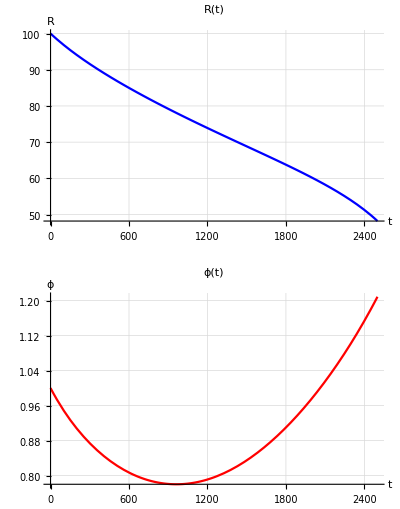

```mathematica
ClearAll["Global`*"]

(*Constants*)
G=20*10^6/3;
w=30*10^-9;
z=3.4*10^*9;
y=2*10^-9;
σ=4.5*10^-3;
Γ=20;
r=400*10^-9;
v=15*10^-9;
k=11250*10^-21;
α=0.058*10^-18/3600;
αt=α/r^3;
P=80*10^3;
Np=2;

(*External X(t)*)
X[t_]:=0;

(*Define d,A-F as functions of R[t],ph[t]*)
d[t_]:=Sqrt[1+R[t]^2-2 (Cos[ph[t]]^2-Sin[ph[t]]*Sqrt[R[t]^2-Cos[ph[t]]^2])];

A1[t_]:=(π (k r^2 Cos[ϕ[t]]^2-4 r^2 σ Cos[ϕ[t]]^2 R[t]^2-8 σ (-1+Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2]) R[t]^4))/(Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2] R[t]^3);

B1[t_]:=(π r (k r Cos[ϕ[t]]+(4 r σ Cos[ϕ[t]]+2 Γ Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2]) R[t]^2) Sin[ϕ[t]])/(Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2] R[t]^2);

C1[t_]:=X-P α+(G Np v w z^2 Cos[ϕ[t]])/(π y);

D1[t_]:=R[t] (-((4 d[t])/((-r+d[t]+R[t]) (r+d[t]+R[t])))+(Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2]+r Sin[ϕ[t]])/(Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sqrt[R[t]^2+r (-r Cos[2 ϕ[t]]+2 Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sin[ϕ[t]])]));

E1[t_]:=(r Cos[ϕ[t]] Sqrt[R[t]^2+r (-r Cos[2 ϕ[t]]+2 Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sin[ϕ[t]])])/Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2];

F1[t_]:=-((4 α d[t]^2)/(π (d[t]^4+(r^2-R[t]^2)^2-2 d[t]^2 (r^2+R[t]^2))));

(*RHS of system*)
Rdot[t_]:=(E1[t]*C1[t]-B1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);
phdot[t_]:=(-D1[t]*C1[t]+A1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);

(*Define ODEs*)
eqns={R'[t]==Rdot[t],ph'[t]==phdot[t],R[0]==100,ph[0]==1};

(*Numerical solution*)sol=NDSolve[eqns,{R,ph},{t,0,2500},MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];

(*Plot R vs t*)
rPlot=Plot[Evaluate[R[t]/.sol],{t,0,2500},PlotLabel->"R(t)",AxesLabel->{"t","R"},PlotStyle->Blue,PlotRange->All,GridLines->Automatic];

(*Plot φ vs t*)
phPlot=Plot[Evaluate[ph[t]/.sol],{t,0,2500},PlotLabel->"ϕ(t)",AxesLabel->{"t","ϕ"},PlotStyle->Red,PlotRange->All,GridLines->Automatic];

(*Display both plots*)
GraphicsGrid[{{rPlot},{phPlot}}]
```